```mathematica
Needs["VectorFieldPlots`"]
```

```mathematica
f1=α/(1+Subscript[X, 2]^n)-Subscript[X, 1];
f2=α/(1+Subscript[X, 1]^m)-Subscript[X, 2];
```

```mathematica
jac={
{D[f1,Subscript[X, 1]],D[f1,Subscript[X, 2]]},
{D[f2,Subscript[X, 1]],D[f2,Subscript[X, 2]]}
}
```

{{-1,-(n α X_2^(-1+n))/((1+X_2^n)^2)},{-(m α X_1^(-1+m))/((1+X_1^m)^2),-1}}

```mathematica
sol=Solve[{f1==0,f2==0}/.{n->1,m->1},{Subscript[X, 1],Subscript[X, 2]}]
```

{{X_1→1/2 (-1-√(1+4 α)),X_2→1/2 (-1-√(1+4 α))},{X_1→-1/2+1/2 √(1+4 α),X_2→1/2 (-1+√(1+4 α))}}

```mathematica
A=Simplify[jac/.m->1/.n->1 /.sol⟦2⟧];
A//MatrixForm
```

(-1 | -(4 α)/(1+√(1+4 α))^2
-(4 α)/(1+√(1+4 α))^2 | -1)

{-(1+√(1+4 α))/(1+2 α+√(1+4 α)),-(1+4 α+√(1+4 α))/(1+2 α+√(1+4 α))}

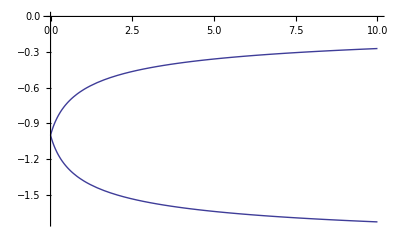

```mathematica
Simplify[Eigenvalues[A]]
Plot[Eigenvalues[A],{α,0,10}]
```

{α→6,n→2,m→2}

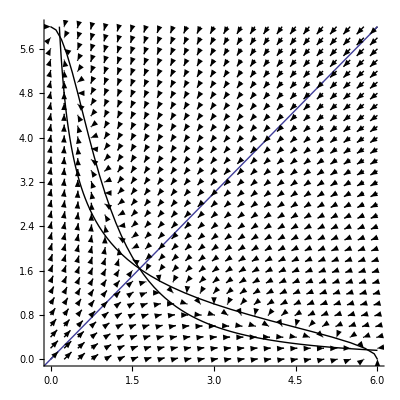

```mathematica
params={α->6,n->2,m->2}
g1=VectorFieldPlot[{f1,f2}/.params,{Subscript[X, 1],0,6,0.25},{Subscript[X, 2],0,6,0.2}];
g2=Plot[x,{x,-0.5,6}];
Show[g,g2,Graphics[
{Line[Table[{α/(1+Subscript[X, 2]^n),Subscript[X, 2]}/.params,{Subscript[X, 2],0,6,0.1}]],
Line[Table[{Subscript[X, 1],α/(1+Subscript[X, 1]^n)}/.params,{Subscript[X, 1],0,6,0.1}]]}
],Axes->True,PlotRange->{{0,6},{0,6}}]
```